## CP8: Partial derivatives and multivariate functions

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Partial derivatives

In Mathematica, the command D[f,x] is also used for calculating first and second partial derivatives of a multivariate function. A special form of this command D[f,{{x,y},2}] will calculate the Hessian of the function f, i.e., a representation of the second partial derivatives (∂^2 f)/(∂x^2), (∂^2 f)/(∂y^2), (∂^2 f)/(∂x∂y) and (∂^2 f)/(∂y∂x).

### Exercise 8-1: Partial derivatives

Calculate the partial derivatives (∂f)/(∂x), (∂f)/(∂y),  (∂^2 f)/(∂x^2), (∂^2 f)/(∂y^2), (∂^2 f)/(∂x∂y) and (∂^2 f)/(∂y∂x) for the following functions:

(a) f(x,y)=x ·cos(2y)

```mathematica
f=x*Cos[2y];
D[f,{x,1}]
D[f,{x,2}]
D[f,{y,1}]
D[f,{y,2}]
D[f,x,y]
```

Cos[2 y]

0

-2 x Sin[2 y]

-4 x Cos[2 y]

-2 Sin[2 y]

(b) f(x,y)=x/(x+y)

```mathematica
f=x/(x+y);
D[f,{x,1}] //Simplify
D[f,{x,2}]//Simplify
D[f,{y,1}]//Simplify
D[f,{y,2}]//Simplify
D[f, {x,1}, {y,1}]//Simplify
```

y/(x+y)^2

-(2 y)/(x+y)^3

-x/(x+y)^2

(2 x)/(x+y)^3

(x-y)/(x+y)^3

(c) f(x,y)=ln(x-y)

```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=Log[x-y]
Derivative[1,0][f][x,y]
Derivative[2,0][f][x,y]
Derivative[0,1][f][x,y]
Derivative[0,2][f][x,y]
Derivative[1,1][f][x,y]
```

1/(x-y)

-1/(x-y)^2

-1/(x-y)

-1/(x-y)^2

1/(x-y)^2

(d) f(x,y)=e^(2x-3y)

```mathematica
Clear[f]
```

```mathematica
f=Exp[2x-3y];
D[f,{x,1}]
D[f, {x,2}]
D[f,{y,1}]
D[f,{y,2}]
D[f, {x,1}, {y,1}]
```

2 ⅇ^(2 x-3 y)

4 ⅇ^(2 x-3 y)

-3 ⅇ^(2 x-3 y)

9 ⅇ^(2 x-3 y)

-6 ⅇ^(2 x-3 y)

### Exercise 8-2: Extremes of a multivariate function

(a) Calculate the optimal conditions, i.e., the temperature x (°C) and relative humidity y (%) that maximize the survival v(x,y)=4y-0.05·(x+x^2-xy+y^2) of the blue poison arrow frog Dendrobatus azureus.

```mathematica
v[x_,y_]:=4*y-0.05*(x+x^2-x*y+y^2)
dvdx=Derivative[1,0][v][x,y];
dvdy=Derivative[0,1][v][x,y];
extrema=Values[Solve[dvdx==0&&dvdy==0,{x,y}]]
```

{{26.,53.}}

```mathematica
H=D[v[x,y], {{x,y},2}];
MatrixForm[H]
```

(-0.1 | 0.05
0.05 | -0.1)

```mathematica
If[Det[H]>0, If[Tr[H]<0, "Maximum", "Minimum"], "Saddle Point"]
```

Maximum

(b) Plot the survival function v(x,y). Hint: use the command Plot3D[].

53.

```mathematica
ps=Plot3D[v[x,y], {x, -100, 100}, {y, 0, 100}, ColorFunction->ColorData["Rainbow"], BoxRatios->{1,1,1}];
pm=ListPointPlot3D[{{extrema[[1,1]],extrema[[1,2]],v[extrema[[1,1]],extrema[[1,2]]]}}, BoxRatios->{1,1,1},PlotStyle->Black];
Show[ps, pm]
```

-Graphics3D-

### Exercise 8-3: Error analysis

The function S(V,d)=5000·V/d^2 describes the wind speed S (m/s) at a distance d  (m) of the eye of a hurricane with volume V (m^3). Consider a hurricane with volume V̄= 6·10^4±1·10^4 m^3 at a distance d̄=3·10^3±1·10^3 m (mean ± stddev)

(a) Estimate the expected wind speed S̄ in km/h from S(V,d). Assuming that wind speeds > 200 km/h can be dangerous, would you evacuate the inhabitants?

```mathematica
s[v_,d_]:=5000*v/(d^2)
meanV=6*10^4;
stdV=1*10^4;
varV=stdV^2;
meanD=3*10^3;
stdD=1*10^3;
varD=stdD^2;
```

As d (distance to the eye of the hurricane) and V (volume of the hurricane) are statistically independent from each other. The estimate of S̄ is as follows

```mathematica
sAtMeanVD=s[meanV, meanD]
N[%]
sAtMeanVDkm=sAtMeanVD*3.6
```

100/3

33.3333

120.

(b) Now use the improved estimator  S̄=S(V,d)+1/2·(∂^2 S)/(∂V^2)·(SD(V))^2+1/2·(∂^2 Sf)/(∂d^2)·(SD(d))^2. How about evacuation in this case?

```mathematica
meanS=s[meanV, meanD]+1/2*Derivative[2,0][s][meanV, meanD]*varV+1/2*Derivative[0,2][s][meanV,meanD]*varD
N[%]
meanSkm=meanS*3.6
```

400/9

44.4444

160.

(c) Also estimate the std deviation of wind speed SD(S)=√(((∂S)/(∂V)·SD(V))^2+((∂S)/(∂d)·SD(d))^2). Are you going to evacuate now?

```mathematica
stdS=Sqrt[(Derivative[1,0][s][meanV, meanD]*stdV)^2+(Derivative[0,1][s][meanV,meanD]*stdD)^2]
stdS*3.6
```

(50 √17)/9

82.4621

The expected wind speed S̄±SD(S) = 160 ± 82 km/h. So wind speed could be larger than 200km/h, evacuation is therefore recommended.

(d) Let us see whether error analysis works well. Draw a large (e.g. 10000) number of random normal variables for V and for d. Compute S(V,d) for each of these random variables, and compare the mean and std deviation to your estimates in (b) and (c). Are they similar? What is the probability that the wind speed exceeds 200 km/h?  Hint: use the Mathematica commands RandomVariate[distr, n] to draw n samples from distribution dist,  NormalDistribution[mean, std] to define a normal distribution with mean mean and standard deviation std and Histogram[] to plot a histogram of the generated values.

```mathematica
distV=RandomVariate[NormalDistribution[meanV, stdV], 10000000];
distD=RandomVariate[NormalDistribution[meanD, stdD],10000000];
distS=3.6*5000*distV/distD^2;
```

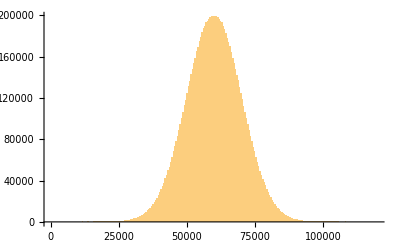

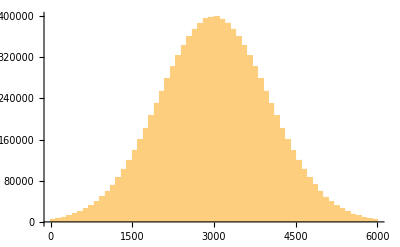

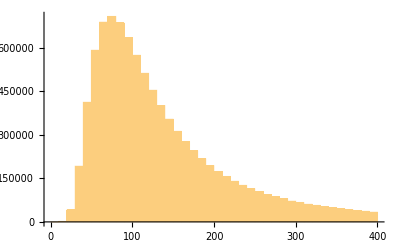

292845.

119.2

4.14571×10^8

200.576

```mathematica
Histogram[distV,{0,120000,500}]
Histogram[distD,{0,6000,100}]
Histogram[distS,{0,400,10}]
Mean[distS]
Median[distS]
StandardDeviation[distS]
Quantile[distS,0.75]
```